```mathematica
1
```

1

```mathematica
.13
```

```mathematica
copyNoteBookFileName
```

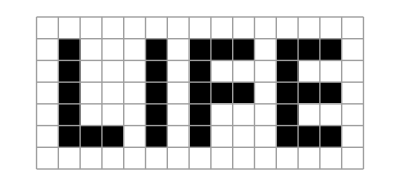
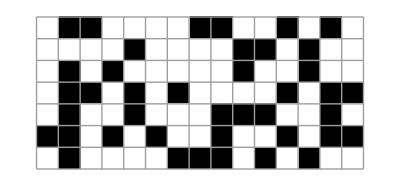
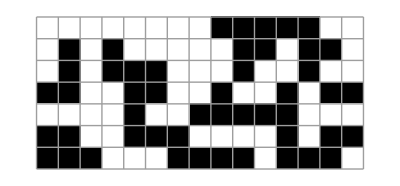
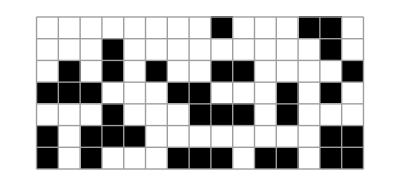
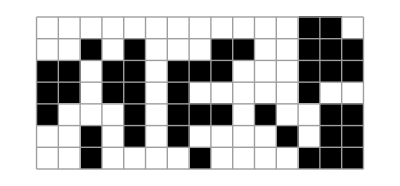
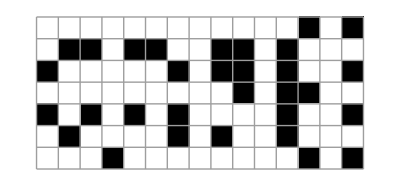
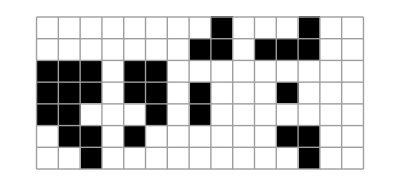
{78.545,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/life.m"];
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];
LIFE=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,updateIJ[LIFE]//lifePlot}]
```

```mathematica
MessageDialog
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf3.m"];

output=StringReplace[updateIJF[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}})],rules];
export="p cnf 48 2015 \n"<>output<>" 0";
ii=Export[NotebookDirectory[]<>"satproblem.txt",export]//Import;
SetDirectory[NotebookDirectory[]];
DeleteFile["satproblem.cnf"];
RenameFile["satproblem.txt","satproblem.cnf"];
ii;
```

```mathematica
Import["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/satproblem1output.txt"]
```

s SATISFIABLE
v -1 2 3 -4 -5 -6 7 -8 -9 0

```mathematica
life33
```

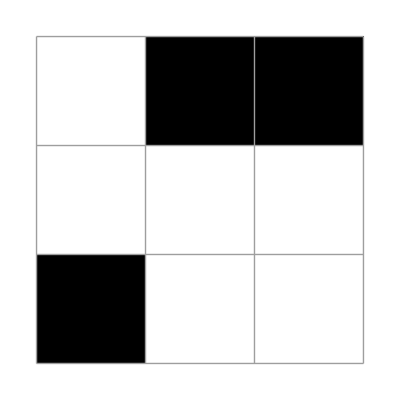
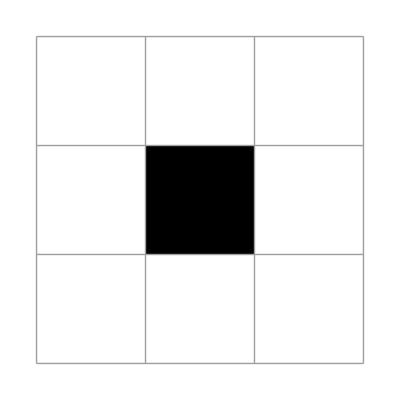

```mathematica
X1=({{0, 1, 1}, {0, 0, 0}, {1, 0, 0}});
plt/@NestList[updateLife[ #]&,
X1,1]
```

```mathematica
|
```

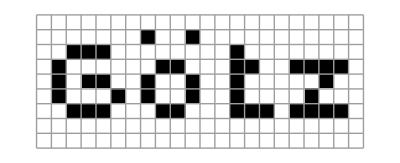
{64.6616,{-Graphics-,{{1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,1},{1,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,1},{0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,1,0,0,0,1,0,1,1,0,0,1,0,0,1},{0,1,0,0,0,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0},{0,0,1,1,0,1,0,0,0,1,1,1,0,1,1,0,1,0,0,1,0,0},{0,1,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1,0,1,1},{0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,0},{1,0,1,0,1,0,1,0,1,1,0,0,0,1,0,0,1,1,1,0,1,0}}}}

```mathematica
lr;Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];
LIFE=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 1, 1, 1, 1, 0}, {0, 1, 0, 1, 1, 0, 0, 1, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 1, 0, 1, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
(*LIFE=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0}, {0, 1, 0, 0, 0, 1, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}});*)
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,lifePlot[XX0=updateIJ[LIFE],9]}]
```

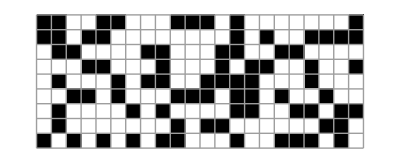
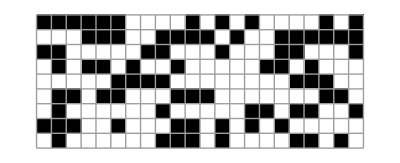
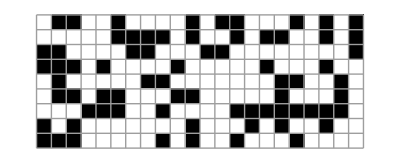
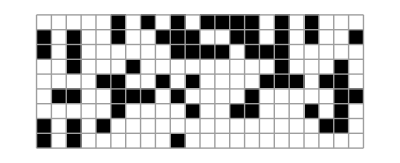
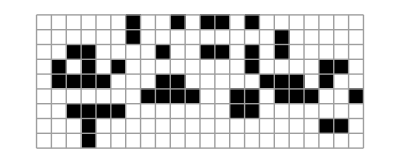
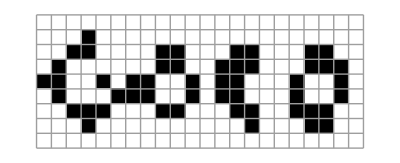
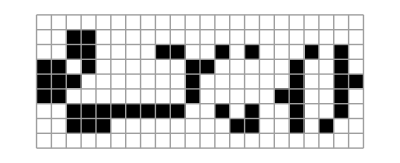
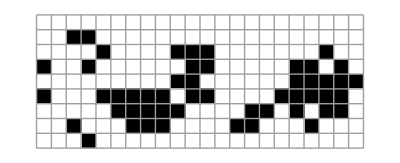
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FRAMES=lifePlot[XX0,42]
```

```mathematica
X0=updateIJ[LIFE];
```

Set::wrsym: Symbol False is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];
updateIJ[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Clear[i,j,x2];
count[{2,3},{{i,j}[[1]],{i,js}[[2]]},x2]
```

```mathematica
lr
```

and::shdw: Symbol and appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
Get[]
```

```mathematica
Clear[x0,x1,x2,x3,x4]CopyToClipboard[BooleanConvert[(and@{Nothing,          ,(x3[i,j]&&count[{2,3},{i,j},x3])~Implies~xp[i,j]
        ,(x3[i,j]&&!count[{2,3},{i,j},x3])~Implies~!xp[i,j]
        ,(!x3[i,j]&&count[{3},{i,j},x3])~Implies~xp[i,j]
        ,(!x3[i,j]&&!count[{3},{i,j},x3])~Implies~!xp[i,j]
}),
"CNF"]];
```